```mathematica
γ =4.0
mtimed= Table[Table[{t,2.Sin[(π t/200)+π k/10]HeavisideTheta[t-00.1]+γ UnitBox[-( t/200)+(k/5)+5]Sin[(π t/200)-π k/5]},{t,0,2000,1}],{k,1,20}]
MatrixForm/@m;
m//MatrixForm
pix=Table[Interpolation[mtimed[[k]],InterpolationOrder->0],{k,1,20}]
```

4.

m

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

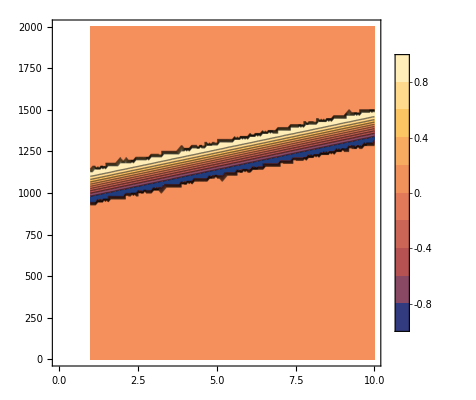

```mathematica
ContourPlot[-HeavisidePi[-( t/200)+5+(k/5)]1.Sin[(π t/200)-π k/5],{k,1,10},{t,0,2000},PlotRange->{1,-1},PlotLegends->Automatic,Exclusions->None]
```

```mathematica
shift=0
pixel=5
pixshift=1
time=2000
Ibias={2,2,2.5,2.5,1.1}
Ibias={0,1.5,2.5,2.5,2}
Monitor[solDetection=NDSolve[
{(*neuron e1*)
Ve1'[t]==Fv[Ve1[t],We1[t]][Ibias[[1]],k,b]+pix[[pixel]][t+shift]+gee Se2[t] +gie Si1[t]+Ibias[[1]],Ve1[0]==0,
We1'[t]==Fw[Ve1[t],We1[t]][a,b],We1[0]==6,
tau Se1'[t]== -Se1[t],Se1[0]==0,
WhenEvent[Ve1[t]==130,{Ve1[t]->c,We1[t]->We1[t]+d,Se1[t]->Se1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron e2*)
Ve2'[t]==Fv[Ve2[t],We2[t]][Ibias[[2]],k,b]+pix[[pixel+pixshift]][t]+gee Se1[t] +gie Si2[t]+Ibias[[2]],Ve2[0]==0,
We2'[t]==Fw[Ve2[t],We2[t]][a,b],We2[0]==6,
tau Se2'[t]== -Se2[t],Se2[0]==0,
WhenEvent[Ve2[t]==130,{Ve2[t]->c,We2[t]->We2[t]+d,Se2[t]->Se2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron i1*)
Vi1'[t]==Fv[Vi1[t],Wi1[t]][Ibias[[3]],k,b]+pix[[pixel+pixshift]][t+shift]+gii Si2[t]+gei Se1[t]+Ibias[[3]],Vi1[0]==0,
Wi1'[t]==Fw[Vi1[t],Wi1[t]][a,b],Wi1[0]==6,
tau Si1'[t]== -Si1[t],Si1[0]==0,
WhenEvent[Vi1[t]==130,{Vi1[t]->c,Wi1[t]->Wi1[t]+d,Si1[t]->Si1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuroni2*)
Vi2'[t]==Fv[Vi2[t],Wi2[t]][Ibias[[4]],k,b]+pix[[pixel]][t]+gii Si1[t]+gei Se2[t]+Ibias[[4]],Vi2[0]==0,
Wi2'[t]==Fw[Vi2[t],Wi2[t]][a,b],Wi2[0]==6,
tau Si2'[t]== -Si2[t],Si2[0]==0,
WhenEvent[Vi2[t]==130,{Vi2[t]->c,Wi2[t]->Wi2[t]+d,Si2[t]->Si2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron out*)
Vo'[t]==Fv[Vo[t],Wo[t]][Ibias[[5]],k,b]+go Se1[t]+go Se2[t],Vo[0]==0,
Wo'[t]==Fw[Vo[t],Wo[t]][a,b],Wo[0]==6,
WhenEvent[Vo[t]==130,{Vo[t]->c,Wo[t]->Wo[t]+d},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"]},
{Ve1,We1,Se1,Ve2,We2,Se2,Vi1,Wi1,Si1,Vi2,Wi2,Si2,Vo,Wo},{t,0,time},Method->{"FixedStep","StepSize"->0.1,"Method"->{"ExplicitRungeKutta"}},Compiled->True,EvaluationMonitor:>(monitor=t)];,monitor]
monitor

Print["Done"]
```

0

5

1

2000

{2,2,2.5,2.5,1.1}

{0,1.5,2.5,2.5,2}

InterpolatingFunction::dmval: Input value {2000.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2000.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

2000.

Done

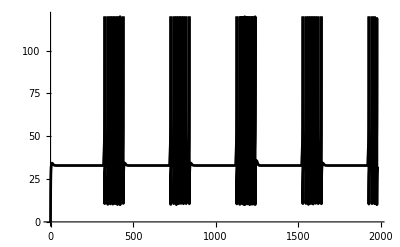

```mathematica
Plot[{(Vo[t]/.solDetection)},{t,0,1980},PlotRange->{0,120},PlotPoints->1000,AspectRatio->1/GoldenRatio,PlotStyle->Black]
```